```mathematica
data=Import["C:\\Users\\Evan\\GitProjects\\weather-prediction\\data2\\fullTest\\EXPERIMENTS.csv"];
data1 = data[[2;;85,All]];
data2 = data[[86;;,All]];
TOLERANCE = 1;
HIDDEN = 2;
DISTANCE = 3;
LEARNING  = 4;
ITERATIONS = 5;
TARGET = 6;
TIME = 7;
EWXAVG=8;
EWXSTD = 9;
GRKAVG=10;
GRKSTD = 11;
```

```mathematica
targets1={{0,Red},{0.5,Green},{1,Blue}};
targets2={{0,RGBColor[0.82,0.25,0.5]},{0.5,RGBColor[0.5,0.8,0.5]},{1,RGBColor[0.5,0.28,0.89]}};
Show[
ListPlot3D[Table[Select[data1,#[[TARGET]]==TAR&][[All,{ITERATIONS, LEARNING,EWXAVG}]],{TAR,targets1[[All,1]]}],AxesLabel->{"Iterations","Learning Rate","Avg. Error"},
PlotStyle->targets1[[All,2]],
PlotLegends->
Table["1-Target Value = "<>ToString[val],{val,targets1[[All,1]]}]
],
ListPlot3D[Table[Select[data2,#[[TARGET]]==TAR&][[All,{ITERATIONS, LEARNING,EWXAVG}]],{TAR,targets2[[All,1]]}],AxesLabel->{"Iterations","Learning Rate","Avg. Error"},
PlotStyle->targets2[[All,2]],
PlotLegends->
Table["2-Target Value = "<>ToString[val],{val,targets2[[All,1]]}]
],
PlotLabel->"Average of error from EWX Data"
]
Show[
ListPlot3D[Table[Select[data1,#[[TARGET]]==TAR&][[All,{ITERATIONS, LEARNING,EWXSTD}]],{TAR,targets1[[All,1]]}],AxesLabel->{"Iterations","Learning Rate","Std. Dev. Error"},
PlotStyle->targets1[[All,2]],
PlotLegends->
Table["1-Target Value = "<>ToString[val],{val,targets1[[All,1]]}]
],
ListPlot3D[Table[Select[data2,#[[TARGET]]==TAR&][[All,{ITERATIONS, LEARNING,EWXSTD}]],{TAR,targets2[[All,1]]}],AxesLabel->{"Iterations","Learning Rate","Std. Dev. Error"},
PlotStyle->targets2[[All,2]],
PlotLegends->
Table["2-Target Value = "<>ToString[val],{val,targets2[[All,1]]}]
],
PlotLabel->"Standard Deviation of error from EWX Data"
]
Show[
ListPlot3D[Table[Select[data1,#[[TARGET]]==TAR&][[All,{ITERATIONS, LEARNING,GRKAVG}]],{TAR,targets1[[All,1]]}],AxesLabel->{"Iterations","Learning Rate","Avg. Error"},
PlotStyle->targets1[[All,2]],
PlotLegends->
Table["1-Target Value = "<>ToString[val],{val,targets1[[All,1]]}]
],
ListPlot3D[Table[Select[data2,#[[TARGET]]==TAR&][[All,{ITERATIONS, LEARNING,GRKAVG}]],{TAR,targets2[[All,1]]}],AxesLabel->{"Iterations","Learning Rate","Avg. Error"},
PlotStyle->targets2[[All,2]],
PlotLegends->
Table["2-Target Value = "<>ToString[val],{val,targets2[[All,1]]}]
],
PlotLabel->"Average of error from GRK Data"
]
Show[
ListPlot3D[Table[Select[data1,#[[TARGET]]==TAR&][[All,{ITERATIONS, LEARNING,GRKSTD}]],{TAR,targets1[[All,1]]}],AxesLabel->{"Iterations","Learning Rate","Std. Dev. Error"},
PlotStyle->targets1[[All,2]],
PlotLegends->
Table["1-Target Value = "<>ToString[val],{val,targets1[[All,1]]}]
],
ListPlot3D[Table[Select[data2,#[[TARGET]]==TAR&][[All,{ITERATIONS, LEARNING,GRKSTD}]],{TAR,targets2[[All,1]]}],AxesLabel->{"Iterations","Learning Rate","Std. Dev. Error"},
PlotStyle->targets2[[All,2]],
PlotLegends->
Table["2-Target Value = "<>ToString[val],{val,targets2[[All,1]]}]
],
PlotLabel->"Standard Deviation of error from GRK Data"
]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

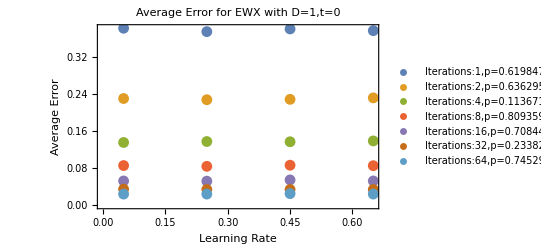

```mathematica
index = GRKSTD;
label="Average Error for EWX with D=1,t=0";
data=data2;
target=1;
fitData=Table[
NonlinearModelFit[
Select[data,And[
#[[TARGET]] == target,
#[[ITERATIONS]]==iter
]&][[All,{LEARNING, index}]],
a * learning + b,
{a,b},
{learning}]["ParameterPValues"][[1]],{iter,{1,2,4,8,16,32,64}}];
ListPlot[
Table[Select[data,And[
#[[TARGET]] == target,
#[[ITERATIONS]]==2^iter
]&][[All,{LEARNING, index}]],{iter,0,6}],
PlotLegends->Table["Iterations:"<>ToString[2^i]<>",p="<>ToString[fitData[[i + 1]]],{i,0,6}],
PlotLabel->label,
FrameLabel->{"Learning Rate", "Average Error"},
Frame->True]
```